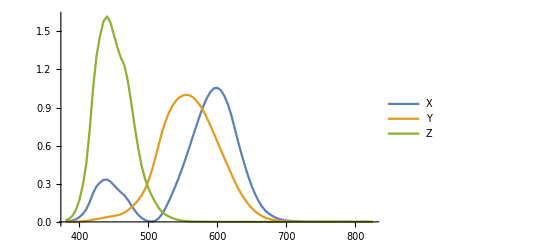

```mathematica
{λ,x,y,z}=Import["http://www.cvrl.org/database/data/cmfs/ciexyzjv.csv"]ᵀ;
ListLinePlot[{{λ,x}ᵀ, {λ,y}ᵀ, {λ,z}ᵀ}, PlotLegends->{"X", "Y", "Z"}]
```

```mathematica
λ = λ 10^-9; (* wavelength is given in nm *)

XYZ[t_] :=
 Module[{h = 6.62607*10^-34,c = 2.998*10^8, k = 1.38065*10^-23},
  {x, y, z}.((2 h c^2)/((-1 + E^((h c/k)/(t λ))) λ^5)) // #/#[[2]] &
  ]
```

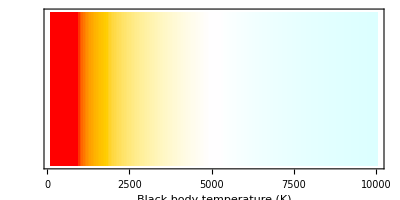

```mathematica
Graphics[
 Table[
  {
   ColorConvert[XYZColor @@ XYZ[i], "RGB"],
   Rectangle[{i, 0}, {i + 50, 5000}]
   },
  {i, 100, 10000, 50}
  ],
 Frame -> True, FrameTicks -> {Automatic, None, None, None},
 FrameLabel -> {"Black body temperature (K)", "", "", ""}
 ]
```